```mathematica
Get["invariant_dmd_v2_8_functions"];
Get["invariant_dmd_v2_8_auxuntested_v1"];
```

```mathematica
Get["dslibrary_v3_3"];
```

## Savefile

```mathematica
savefile = "competing_hopf";
```

## Temporal parameters

0 usually - If delayed, set appropriately

```mathematica
ndelays = 0;

tinit = 0;
npts = 6; (* How many points to sample the limit cycle on ?*)
ncopies = 4;
```

#### Choice of DS

```mathematica
(* Create a separate one for each DS*)
hopfparams = {1/3,2/3(* Radius of limit cycle *),2π (* ω : Angular frequency of LC*)};

tsamp = ((2π)/hopfparams[[-1]])/npts;

localhopffield[t_,{r_,θ_}]:= competinghopffield[t,{r,θ},hopfparams]

vfield = localhopffield;
(* Did not know a better way to do ICs without distrubing the code that follows *)
(* ssdim : Implicit via Length@icrange *)
(* chosenputty: Use to convert coordinates from the ODE version *)
limitcyclesafety = 3;
{icseeds,icrange,chosenputty} = {53, {{0,1},{-π,π}},rhophi2xy };
```

### Tolerances

```mathematica
(* Tolerance *)
sigtols = {10^-8,10^-12}; (* Singular values *)
restols = {10^-8,10^-12};(* greaterabsrelcheck *)
```

### Flavours

Switches for the constant eigenfunction && the delay constraints (You need to put the constant function in userhead !!!) : Set True to activate

#### User defined functions

```mathematica
(* AppendTo[userlist,(*Desired fheads*)];*)
userparams = {};
```

#### User defined constraints

Should be a LIST of matrices !!!

```mathematica
(* Geometric constraints *)
invsamplesets ;
(* Functional constraints *)
ipfuns(**);
opfuns(**);
rawuserlist = {};
```

#### Test constraints

```mathematica
testinvsamplesets=N@get2LChopfinvsamplesets[hopfparams,tsamp,npts,ncopies];
testipfuns;
testopfuns;
```

## Must use this version !!!!

```mathematica
icsconwrap4modifiedoneshot[ics_,{{construct_,basistruct_,invsamplesets_,testinvsamplesets_},{userparams_,rawuserlist_,ipfuns_,opfuns_,testipfuns_,testopfuns_}}]:=modifiedoneshot[ndelays,tinit,tsamp,vfield,ics,chosenputty,sigtols,restols,flavour,flavourparams,construct,basistruct,userparams,rawuserlist,invsamplesets,ipfuns,opfuns,testinvsamplesets,testipfuns,testopfuns,boxflavourparams];
```

## Actual test

#### Seems to have a lower evalthreshold...

```mathematica
getefgrubvecs[amat_,{w_},cmat_,dmat_,sigtols_,teigsys_]:=Module[{m= Length@amat,mii,xmat,ymat,evalthreshold = 10^-12},
mii = Pick[teigsys[[2]],Negative[(Abs@(teigsys[[1]] - w))-evalthreshold]];
If[mii ≠ {},
mii = miiᵀ;
xmat = cmatᵀ.mii;
ymat = mii;
((coredmd[xmat,ymat,{},sigtols,"direct"])[[1]])ᵀ,
Print["No eigenspace found"];
0*cmatᵀ
]
];
```

```mathematica
boxranges = {{-1,1},{-1,1}};
centercounts = {{45,45},{15,15}(* Must be the same as the first to ensure that the scaling is correctly done for trigtri *)};
nsampsperbox = {3,3};
flavour = "boxfuns";

(* How muich of the fringe be included in the plots*)
plotscalefactor = 1.1;
```

### Sampling from a distribution

#### Sample points

```mathematica
boxflavourparams = {boxranges,centercounts[[-1]]};
flavourparams ={boxranges,centercounts[[1]]};
```

```mathematica
detics =N@DeleteCases[CoordinateTransform[{"Cartesian"->"Polar",2},(*Enter the XY corrdinate matrix here *)  Join@@MapThread[(#1@(getdetseeds4Box[boxranges,#2,#3]))&,{{#&,puttheseoutright[#,boxflavourparams]&},centercounts,nsampsperbox}]],{_,Indeterminate}];
ncompsamples = Length@detics;
```

ArcTan::indet: Indeterminate expression ArcTan[0,0] encountered.

#### Plot points

```mathematica
plotcc = centercounts[[1]];
plotspb = nsampsperbox[[1]];
plotbrs  = plotscalefactor *boxranges;
plotparams = {plotbrs,plotcc,plotspb};
```

```mathematica
(*----------ODE in sampled coordinates ----------*)
plotics0 = N@DeleteCases[CoordinateTransform[{"Cartesian"->"Polar",2},(*Enter the XY corrdinate matrix here *)  getdetseeds4Box@@plotparams],{_,Indeterminate}];
```

```mathematica
plotics =Select[plotics0,
( #[[1]] > 10^-8)&] ;
```

#### Expected spectrum

```mathematica
(* Keeping it as is to not have to untangle the coordinate transformation as well.*)
```

```mathematica
jacobevals = Map[(Derivative[0,{1,0}][localhopffield][t,{#,0}])[[1]]&,Most[hopfparams]];
expectedevalues  = Exp[jacobevals*tsamp];
```

### Le test variations

```mathematica
neededbaggage = {detics,plotics,sigtols,tsamp,ncompsamples,ndelays,flavourparams,expectedevalues,ncopies};
```

```mathematica
activecons;
passivecons = {userparams,rawuserlist,ipfuns,opfuns,testipfuns,testopfuns};
```

#### Stuff to vary the constraints (The plots and ef access may vary !!!)

```mathematica
getlistplotdata[evec_,plotics_,ploticslifted_,mod_]:=Join[plotics,{Map[mod,(evec.ploticslifted)]}ᵀ,2];
```

```mathematica
getevalandefplots[activecons_,passivecons_,{detics_,plotics_,sigtols_,tsamp_,ncompsamples_,ndelays_,flavourparams_,expectedevalues_,ncopies_}]:=Module[{testamat,testq0,testmexparams,testi2bdmparams,testkerrors,testconerrors,testresidue,ploticslifted,eigsys,testefgrubvecs,specplot,trueplotics},
{{testamat,{testq0,testmexparams,testi2bdmparams}},{testkerrors,testconerrors,testresidue}} =icsconwrap4modifiedoneshot[detics,{activecons,passivecons} ];
Print[{tsamp,ncompsamples,ndelays,flavourparams,testkerrors,testconerrors,testresidue}];
ploticslifted = liftaset[plotics,testi2bdmparams,testmexparams];
(*--LC specific stuff--*)
trueplotics = CoordinateTransform[{"Polar"->"Cartesian",2}, plotics ];
eigsys = Eigensystem[testamatᵀ];
(*-------------------------PREP 4 SPEC PLOTS----------------------*)
discevals =eigsys[[1]];
disclattice = generatediscretetimelattice[expectedevalues,8];
{contevals, contlattice} = 1/tsamp*Log@{discevals,disclattice};
(* Discrete time SPEC PLOT *)
discspecplot =Map[getdiscspecplot[discevals,#]&,{expectedevalues,disclattice}];
(* Continuous time SPEC PLOT*)
contspecplot = getcontspecplot[contevals, contlattice];
(* Compute eigenfunctions *)
rawtestefgrubvecs = invset2efs[activecons[[4]],testq0,testamat,sigtols,eigsys];
(* Some added post-processing coz this is a limit cycle *)
testefgrubvecs  = {rawtestefgrubvecs[[1]],Plus@@rawtestefgrubvecs[[Range[ncopies] + 1]],Plus@@rawtestefgrubvecs[[-1*Range[ncopies]]]};
(* SPEC PLOTS *)
Print[discspecplot];
Print[contspecplot];
(*--Plot efs ----*)
Print@Table[ListDensityPlot[getlistplotdata[testefgrubvecs[[i,1]],N@trueplotics,ploticslifted,Abs],PlotRange->All,PerformanceGoal->"Quality",PlotLegends->Automatic,LabelStyle->Directive[Bold,Black,Medium],ImageSize->Large],{i,(* COz we have three distinct invariants*)3}]
];
```

{{{45,45},{15,15}},{3,3}}

{1/6,20160,0,{{{-1,1},{-1,1}},{45,45}},{7.91879,0},{{2.8672×10^-15,4.42005×10^-13},{3.80188×10^-15,3.80188×10^-15}},1998.98}

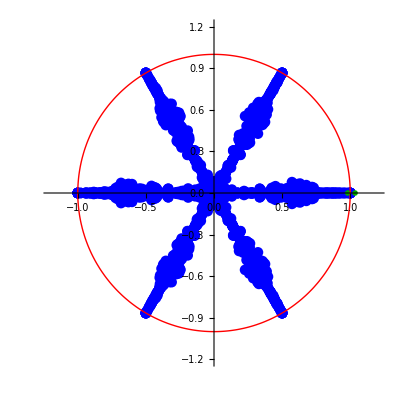
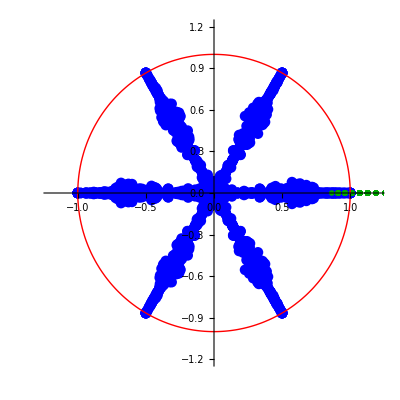

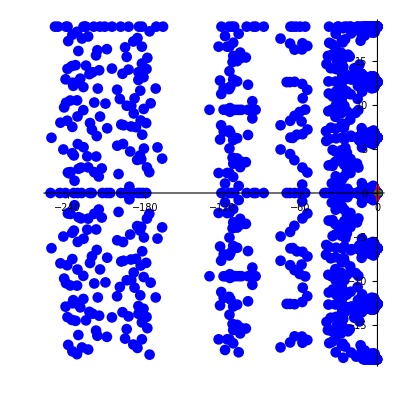

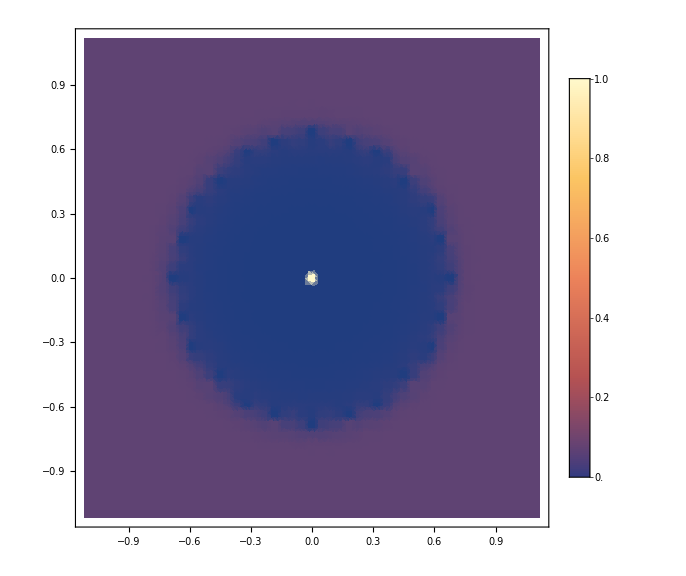
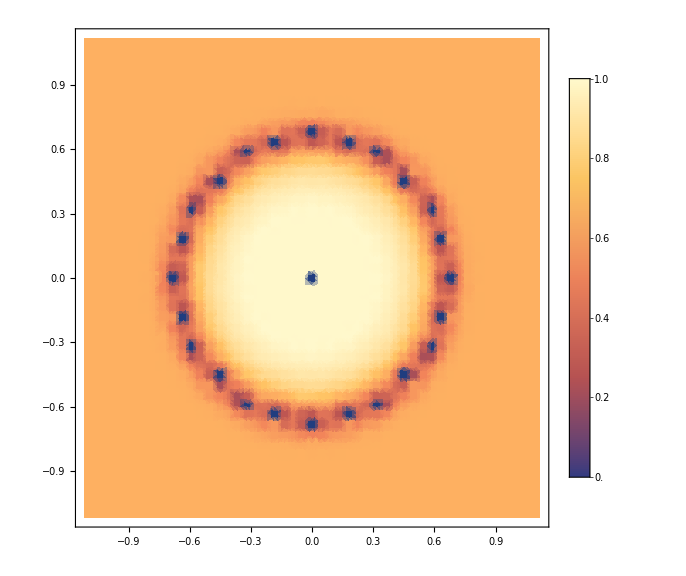
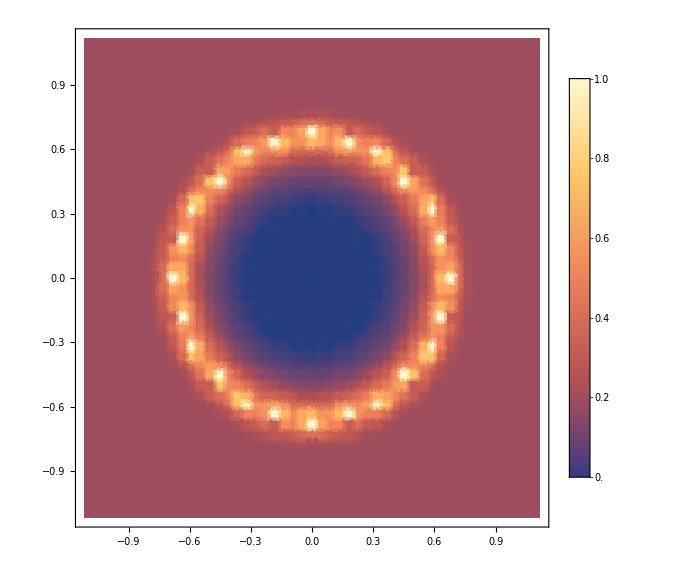

{1/6,20160,0,{{{-1,1},{-1,1}},{45,45}},{8.32214,0},{{1.01523,104.855},{4.84108×10^-16,4.84108×10^-16}},1974.07}

No eigenspace found

No eigenspace found

No eigenspace found

«2 more identical outputs»

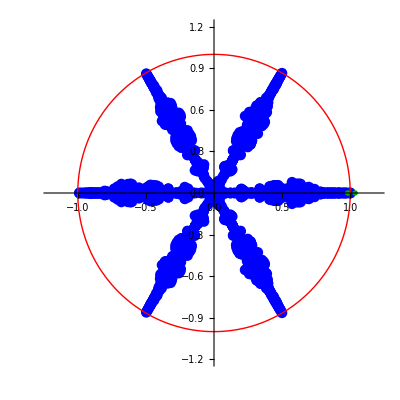
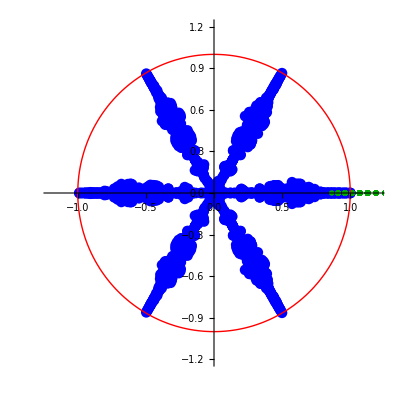

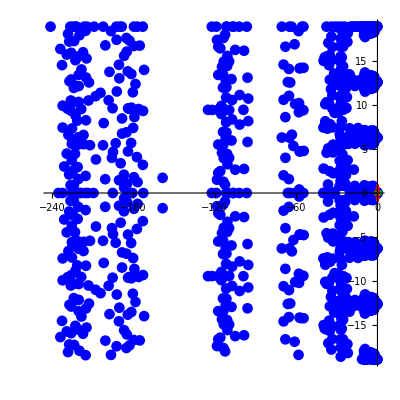

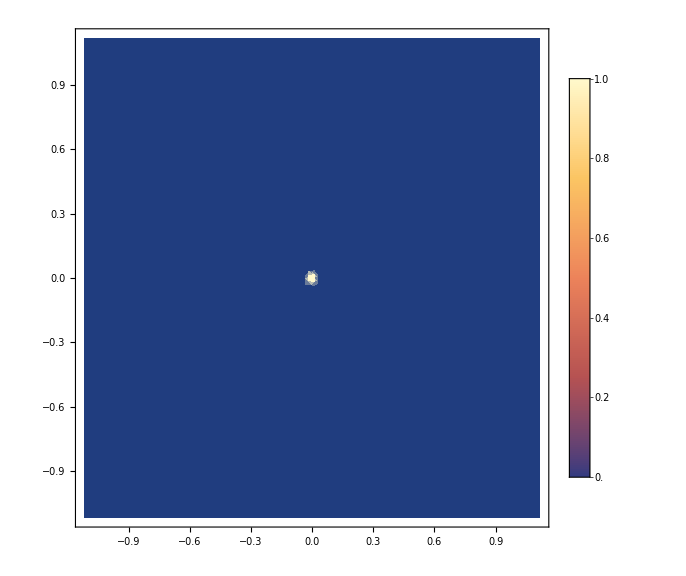
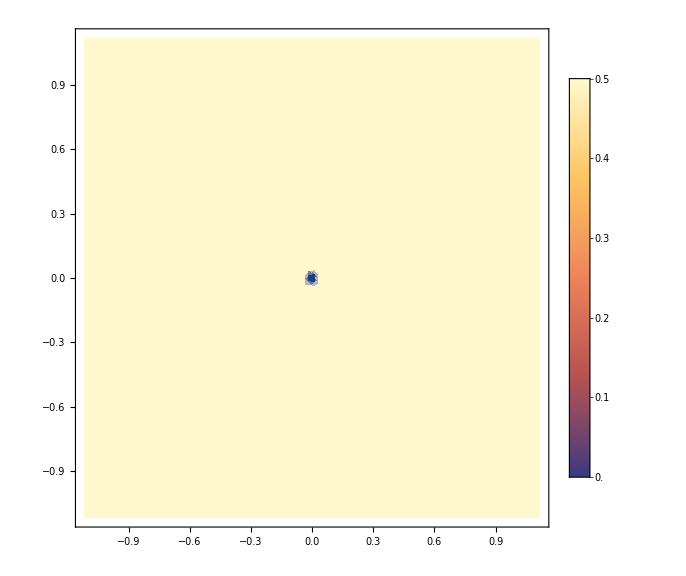
{-Graphics-,-Graphics-,-Graphics-}

{1/6,20160,0,{{{-1,1},{-1,1}},{45,45}},{1.06066,0},{{1.01757,104.855},{}},1974.07}

No eigenspace found

No eigenspace found

No eigenspace found

«2 more identical outputs»

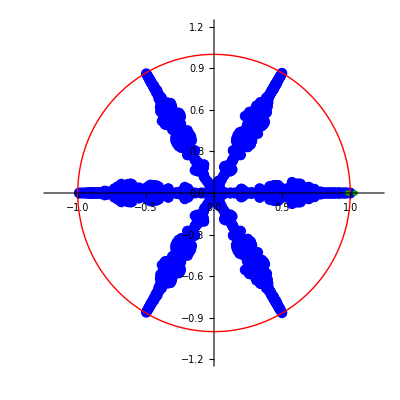
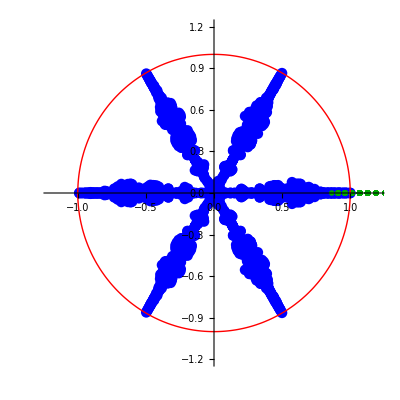

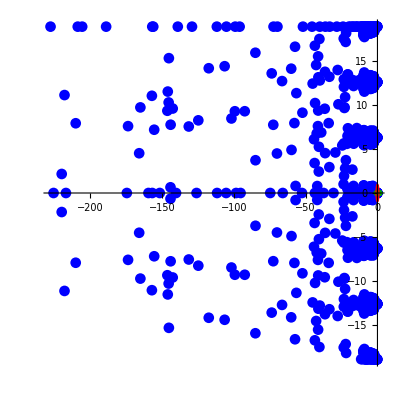

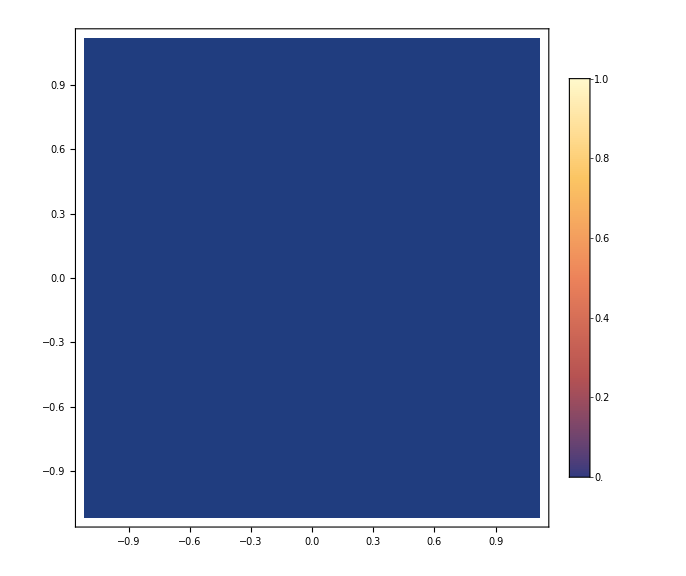
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Print[{centercounts,nsampsperbox}]
goodplotgrub=MapThread[getevalandefplots[{#1,#2,#3,testinvsamplesets},passivecons,neededbaggage]&,{{True,True,False},{True,True,False},{testinvsamplesets,{},{}}}];
(*DumpSave["competinghopf_45x45_15x15_3x3",goodplotgrub];*)
```